## University of MS, Phys. 709 Fall 2018 Problem Set 1 supplement

Author: Leo C. Stein (lcstein@olemiss.edu)
Date: Fall 2018

## FW 1.9

```mathematica
V[r_]:=-λ/r Exp[-r]
Veff[r_]:=V[r]+ℓ^2/(2 r^2)
```

```mathematica
D[Veff[r],r];
dVeffdr=Collect[%,{Exp[__]},Simplify]
```

-ℓ^2/r^3+(ⅇ^-r (1+r) λ)/r^2

```mathematica
Simplify[dVeffdr==0,Assumptions->{λ>0,ℓ>0,r>0}]
```

ⅇ^r ℓ^2==r (1+r) λ

```mathematica
FW19Plot[α_]:=Plot[{Exp[r],r(1+r) α},{r,0,4},PlotRange->{0,20},Frame->True,PlotLegends->{"e^r",ToString[α]<>"r(1+r)"},FrameLabel->{"r",None,"α="<>ToString[α],None}]
```

```mathematica
Manipulate[FW19Plot[α],{{α,1},0,2}]
```

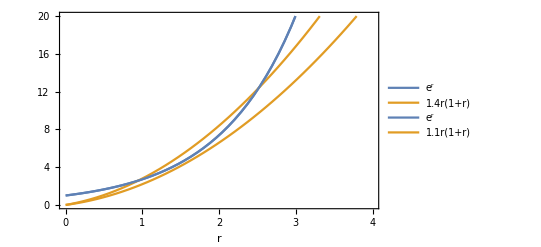

```mathematica
Show[FW19Plot[1.4],FW19Plot[1.1],FrameLabel->"r"]
Export[NotebookDirectory[]<>"FW1_9.pdf",%];
```

```mathematica
Veff''[r]==0/.{Exp[-r]->expMinusr}
First@Solve[%,expMinusr]
Veff'[r]==0/.{Exp[-r]->expMinusr}/.%
rDoubleRootSol=Last@Solve[%,r]
λCritSol=First@Solve[{Veff'[r]==0}/.rDoubleRootSol,λ]//Simplify
%//N
```

(3 ℓ^2)/r^4-(2 expMinusr λ)/r^3-(2 expMinusr λ)/r^2-(expMinusr λ)/r==0

{expMinusr→(3 ℓ^2)/(r (2+2 r+r^2) λ)}

-ℓ^2/r^3+(3 ℓ^2)/(r^3 (2+2 r+r^2))+(3 ℓ^2)/(r^2 (2+2 r+r^2))==0

{r→1/2 (1+√5)}

{λ→(-2+√5) ⅇ^(1/2 (1+√5)) ℓ^2}

{λ→1.19053 ℓ^2}

```mathematica
λcrit=λ/.λCritSol/.ℓ->1
```

(-2+√5) ⅇ^(1/2 (1+√5))

```mathematica
λs={1.1,λcrit,1.4};
```

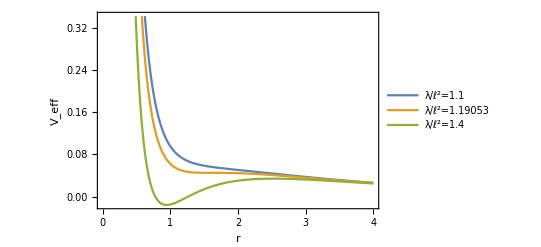

```mathematica
Plot[Evaluate[Veff[r]/.{λ->λs,ℓ->1}],{r,0,4},Frame->True,FrameLabel->{"r","V_eff"},PlotLegends->(("λ/ℓ^2="<>ToString@N@#)&/@λs)]
Export[NotebookDirectory[]<>"FW1_9_Veff.pdf",%];
```